We will calculate the log negativity of a two-mode squeezed vacuum (TMSV) state via the covariance matrix.
We define the TMSV state in the same way as Ulf (p168 eqn 7.21)
1/(cosh(r))∑_(n=0)^∞ (tanh(r))^n|n,n⟩
The covariance matrix Γ_{TMSV} of the TMSV state is given by

```mathematica
tmsv[v_]:={{v, 0, √(v^2-1),0},
{0, v, 0, -√(v^2-1)},
{√(v^2-1),0,v,0},
{0,-√(v^2-1),0,v}};
MatrixForm[tmsv[v]]
```

(v | 0 | √(-1+v^2) | 0
0 | v | 0 | -√(-1+v^2)
√(-1+v^2) | 0 | v | 0
0 | -√(-1+v^2) | 0 | v)

where v := Cosh[2r], and r quantifies the squeezing.

The symplectic eigenvalues may be calculated in the usual way (Weedbrook2012, just after eqn44) as the  absolute value of the eigenvalues of i Ω Γ, where Γ is the covariance matrix.

```mathematica
ω = {{0,1},{-1,0}};
zeroes = {{0,0},{0,0}};
omega4 = ArrayFlatten[{{ω, zeroes},{zeroes, ω}}];
```

The matrix Ω is:

```mathematica
MatrixForm[omega4]
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

Therefore the symplectic eigenvalues of Γ_{TMSV} are

```mathematica
sympEvals[v_]:=Abs[Eigenvalues[ⅈ* omega4.tmsv[v]]]//FullSimplify
sympEvals[v]
```

{1,1,1,1}

which is what we saw earlier. 

To calculate the Log negativity we require the partial transpose of Γ_{TMSV}. It can be shown that the partial transpose takes a particularly nice form in phase space (Simon2000). In particular, in order to take the partial transpose with respect to mode B, one simply flips the signs of all b momenta. (see the discussion following eqn.18 in Simon2000). 
One may also peruse Adesso2007 which has some nice discussions about this, but note that he makes a mistake/typo in how his partial transpositions are explicitly defined.

For our TMSV covariance matrix, the partial transposition gives:

```mathematica
tmsvPT[v_]:={{v, 0, √(v^2-1),0},
{0, v, 0, √(v^2-1)},
{√(v^2-1),0,v,0},
{0,√(v^2-1),0,v}};
```

```mathematica
Grid[{{Labeled[tmsv[v]//MatrixForm, "regular covariance matrix"], Labeled[tmsvPT[v]//MatrixForm, "with partial transpose"]}}]
```

(v | 0 | √(-1+v^2) | 0
0 | v | 0 | -√(-1+v^2)
√(-1+v^2) | 0 | v | 0
0 | -√(-1+v^2) | 0 | v)regular covariance matrix | (v | 0 | √(-1+v^2) | 0
0 | v | 0 | √(-1+v^2)
√(-1+v^2) | 0 | v | 0
0 | √(-1+v^2) | 0 | v)with partial transpose

Note that once the covariance matrix is in standard form, one may work entirely in terms of its global invariants which are particularly easy to derive on pen and paper. See Weedbrook2012 or Adesso2007, where they calculate explicitly in terms of the Determinant and the Seralian.

Let’s find the symplectic eigenvalues of Γ_{TMSV}^{PT}

```mathematica
sympEvalsPT[v_]:=Abs[Eigenvalues[ⅈ* omega4.tmsvPT[v]]]//FullSimplify
sympEvalsPT[v]
```

{√Abs[1-2 v^2-2 √(v^2 (-1+v^2))],√Abs[1-2 v^2-2 √(v^2 (-1+v^2))],√Abs[1-2 v^2+2 √(v^2 (-1+v^2))],√Abs[1-2 v^2+2 √(v^2 (-1+v^2))]}

which are no longer all unity. Plotting,

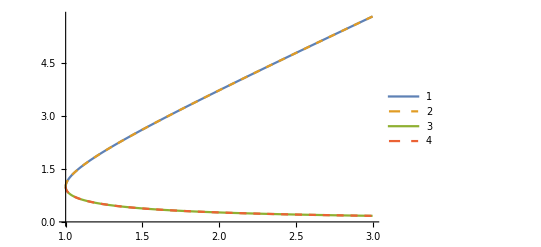

```mathematica
Plot[
Evaluate[sympEvalsPT[v]],
{v,1,3}, PlotStyle->{,Dashed,,Dashed},
PlotLegends->{1,2,3,4}
]
```

we see that some of them are <1, which is what we want. The two in question are:

```mathematica
sympEval3[v_]:=√Abs[1-2 v^2+2 √(v^2 (-1+v^2))]
sympEval4[v_]:=√Abs[1-2 v^2+2 √(v^2 (-1+v^2))]
```

from which the Logarithmic negativity (Weedbrook2012, eq. 62) may be calculated:

```mathematica
logNegativity[v_]:=-Log[sympEval3[v]](* - Log[sympEval4[v]]*)
```

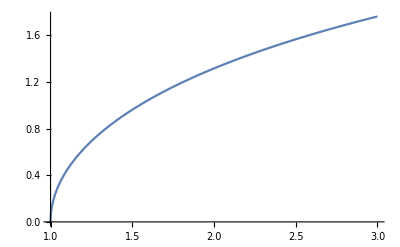

```mathematica
Plot[
logNegativity[v]
,
{v,1,3}
]
```

So we see that increasing v increases the entanglement between modes 1 and 2. Equivalently, in terms of squeezing parameter r:

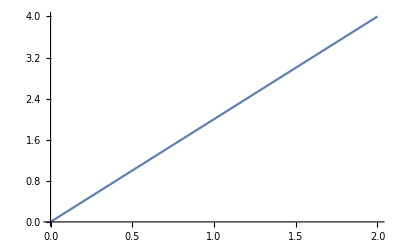

-Graphics-

```mathematica
Plot[
logNegativity[Cosh[2r]]
,
{r,0,2}
]
```

```mathematica
logNegativity[Cosh[2 * 3.8]]
```

7.60032

```mathematica
logNegativity[Cosh[ 2 * 0.59]]
```

1.18

```mathematica
n2r[barn_]:=ArcSinh[√barn]
```

```mathematica
logNegativity[Cosh[2 * n2r[18.0]]]
```

4.30388

```mathematica
n2r[0.44]
```

0.622363

```mathematica
FindRoot[logNegativity[Cosh[2 * n2r[x]]]-1.25==0, {x, 0, 2}]
```

{x→0.444212}

Some notes

1) The symplectic eigenvalues always appear in pairs. Therefore, I am not sure whether one should take both symplectic eigenvalues from a pair into the definition of logarithmic negativity. It will simply scale the log negativity, but may be worth bearing in mind when comparing results with different papers.

2) Different authors may have slightly different forms for their covariance matrices. The discrepancy has caused me a lot of headaches in the past, but it is usually to with how they define x and p operators in terms of creation and annihilation (i.e. do we have 1/sqrt(2), 1/2 or 1). The covariance matrix I used above is taken from Weedbrook2012 so uses their convention.

3) Working in terms of the covariance matrix is equivalent to working in terms of Gaussian Wigner functions - indeed, one may derive the Partial Transpose for a covariance matrix from the definition of the Wigner function. I think Simon2000 does this, or at least alludes to this.

4) See Adesso2007 (and many of his later papers) for more specific and analytical treatments of these things. He tends to work in terms of global invariants of the covariance matrix, which are expressed in terms of determinants of its constituent block matrices.

#### References

Weedbrook2012 - Gaussian Quantum Information, C. Weedbrook et. al., Rev. Mod. Phys 84, (2012)
Adesso2007 - Entanglement of Gaussian States, G. Adesso PhD Thesis, http://arxiv.org/abs/quant-ph/0702069
Simon2000 - Peres-Horodecki Separability Criterion for Continuous Variable Systems, R. Simon, Phys. Rev. Lett. 84, (2000). https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.84.2726
Ulf’s book - Essential Quantum Optics